```mathematica
Question 10
```

```mathematica
(a)
```

```mathematica
Real Part
```

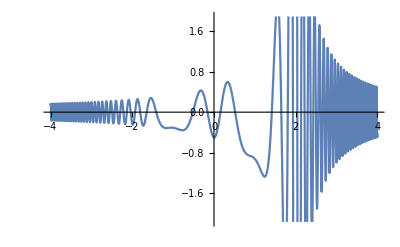

```mathematica
Plot[(Cos[10*(t^3/3 -t)]/(t-2)),{t,-4,4}]
```

```mathematica
Imaginary Part
```

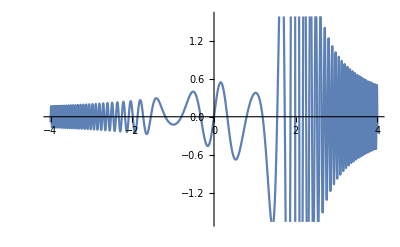

```mathematica
Plot[(Sin[10*(t^3/3 -t)]/(t-2)),{t,-4,4}]
```

```mathematica
b)
```

```mathematica
At t=1
```

```mathematica
r[xi_,eta_]:=xi^3-3*xi*eta^2-3*xi+2;
Solve[r[xi,eta]==0,eta]
```

{{eta→-((-1+xi) √(2+xi))/(√3 √xi)},{eta→((-1+xi) √(2+xi))/(√3 √xi)}}

```mathematica
et1[xi_]:=-((-1+xi) √(2+xi))/(√3 √xi);
```

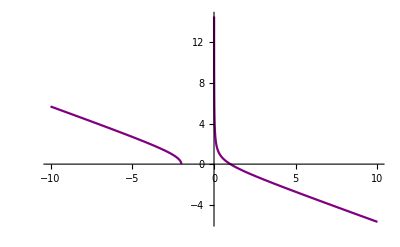

```mathematica
Graph1=Plot[et1[xi],{xi,-10,10},PlotStyle->Purple]
```

```mathematica
et2[xi_]:=((-1+xi) √(2+xi))/(√3 √xi);
```

```mathematica
et2'[1]
```

1

```mathematica
Limit[xi+et2[xi],xi->Infinity]
```

lim_(xi→∞) (xi+et2[xi])

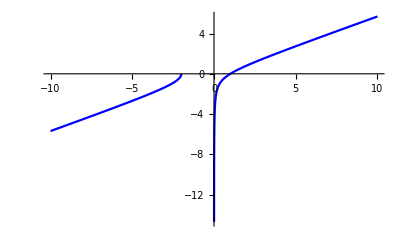

```mathematica
Graph2=Plot[et2[xi],{xi,-10,10},PlotStyle->Blue]
```

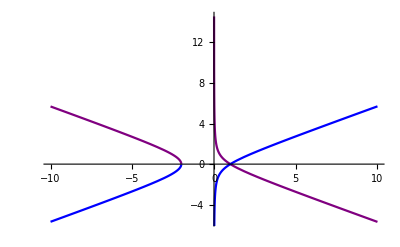

```mathematica
Show[Graph1,Graph2]
```

```mathematica
At t=-1
```

```mathematica
k[xi_,eta_]:=xi^3-3*xi*eta^2-3*xi-2;
```

```mathematica
Solve[k[xi,eta]==0]
```

{{eta→-(√(-2+xi) (1+xi))/(√3 √xi)},{eta→(√(-2+xi) (1+xi))/(√3 √xi)}}

```mathematica
et3[xi_]:=-(√(-2+xi) (1+xi))/(√3 √xi);
```

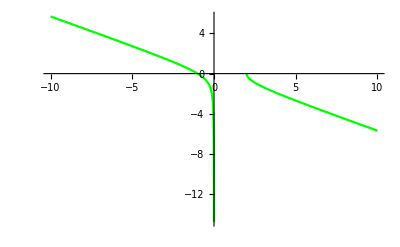

```mathematica
Graph3=Plot[et3[xi],{xi,-10,10},PlotStyle->Green]
```

```mathematica
et4[xi_]:=(√(-2+xi) (1+xi))/(√3 √xi);
```

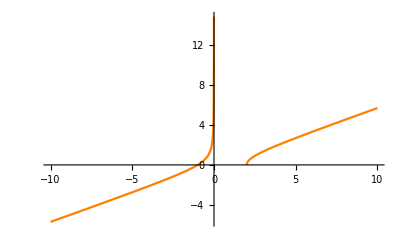

```mathematica
Graph4=Plot[et4[xi],{xi,-10,10},PlotStyle->Orange]
```

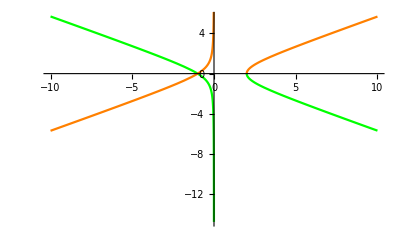

```mathematica
Show[Graph3,Graph4]
```

```mathematica
All Constant Phase Contours
```

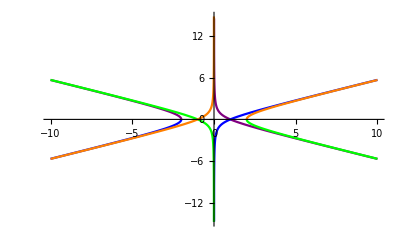

```mathematica
Show[Graph1,Graph2,Graph3,Graph4,PlotRange->All]
```

```mathematica
Real Part Density Plots
```

```mathematica
ClearAll[eta,xi]
```

```mathematica
RealPart[xi_,eta_]:=-xi^2*eta+((eta^3)/3)+eta;
```

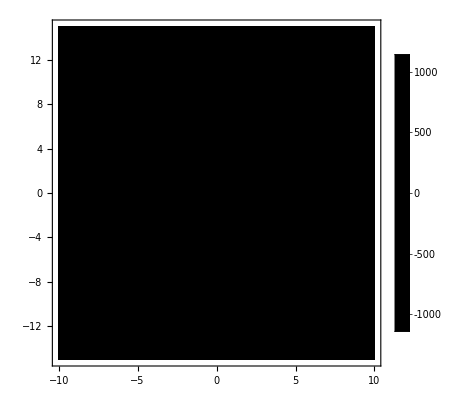

```mathematica
Density=DensityPlot[RealPart[xi,eta],{xi,-10,10},{eta,-15,15},PlotLegends->Automatic,PlotTheme->"Monochrome"]
```

```mathematica
Everything Together
```

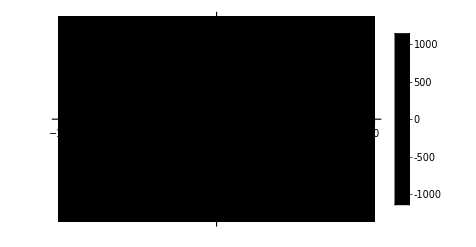

```mathematica
Show[Graph1,Graph2,Graph3,Graph4,Density,PlotRange->All]
```

We see that the paths corresponding to the steepest descent are these

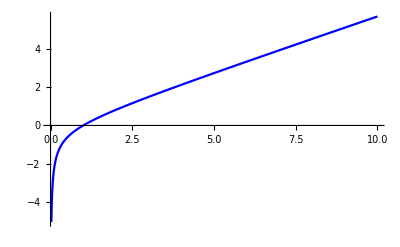

```mathematica
Graph5=Plot[et2[xi],{xi,0,10},PlotStyle->Blue]
```

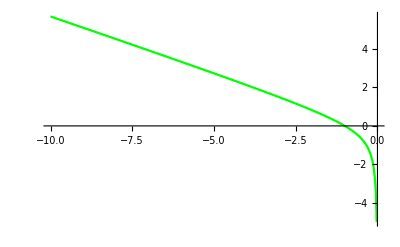

```mathematica
Graph6=Plot[et3[xi],{xi,-10,0},PlotStyle->Green]
```

Therefore, we have

```mathematica
Show[Graph5,Graph6,Density,PlotRange->All]
```

-Graphics-

```mathematica
c)
```

```mathematica
T Function for ξ>0
```

```mathematica
T1[xi_]:=xi+I*(-1+xi)*((2+xi)^(1/2))/((3*xi)^(1/2));
```

```mathematica
T1[xi]
```

xi+(ⅈ (-1+xi) √(2+xi))/(√3 √xi)

```mathematica
T Function for ξ<0
```

```mathematica
T2[xi_]:=xi-(√(-2+xi) (1+xi))/(√3 √xi)*I
T2[xi]
```

xi-(ⅈ √(-2+xi) (1+xi))/(√3 √xi)

```mathematica
Numerical Integration Routine
```

For the positive part we integrate like so

```mathematica
NIntegrate[T1'[xi]*Exp[I*10*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-a),{xi,0,Infinity}]
```

And on the negative part we integrate like so

```mathematica
NIntegrate[T2'[xi]*Exp[I*10*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-a),{xi,-Infinity,0}]
```

Our T functions change depending on the sign of ξ with T2 for negative and T1 for positive.

```mathematica
Real and Imaginary Graphs, ξ>0 with a=2 and x=10
```

General::munfl: Exp[-3.78236×10^6-6.66667 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

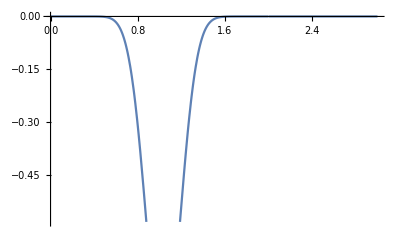

```mathematica
Plot[Re[Exp[I*10*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-2)],{xi,0,3}]
```

General::munfl: Exp[-3.78236×10^6-6.66667 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

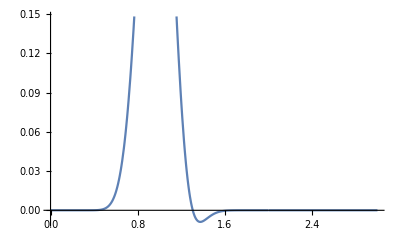

```mathematica
Plot[Im[Exp[I*10*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-2)],{xi,0,3}]
```

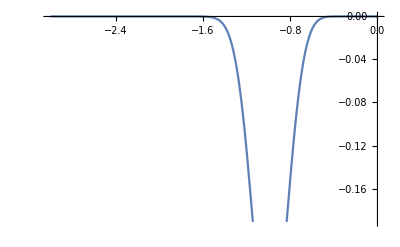

```mathematica
Real and Imaginary Parts,ξ<0 with a=2,x=10
```

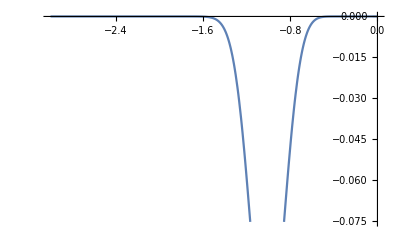

```mathematica
Plot[Im[Exp[I*10*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-2)],{xi,-3,0}]
```

```mathematica
Real Plots Together
```

General::munfl: Exp[-3.78236×10^6-6.66667 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

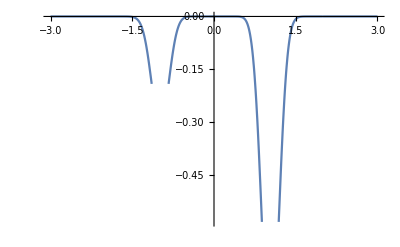

```mathematica
Show[Plot[Re[Exp[I*10*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-2)],{xi,-3,0}],Plot[Re[Exp[I*10*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-2)],{xi,0,3}],PlotRange->All]
```

```mathematica
Imaginary Plots Together
```

General::munfl: Exp[-3.78236×10^6-6.66667 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

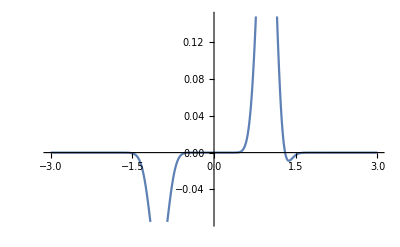

```mathematica
Show[Plot[Im[Exp[I*10*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-2)],{xi,-3,0}],Plot[Im[Exp[I*10*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-2)],{xi,0,3}],PlotRange->All]
```

```mathematica
f(2,10) with ξ>0
```

```mathematica
Wanted1=NIntegrate[T1'[xi]*Exp[I*10*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-2),{xi,0,Infinity}]
```

-0.506287-0.236361 ⅈ

```mathematica
f(3,10) with ξ>0
```

```mathematica
Test1=NIntegrate[T1'[xi]*Exp[I*10*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-3),{xi,0,Infinity}]
```

-0.256651-0.112243 ⅈ

```mathematica
f(2,10) with ξ<0
```

```mathematica
Wanted2=NIntegrate[T2'[xi]*Exp[I*10*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-2),{xi,-Infinity,0}]
```

-0.169831+0.0770556 ⅈ

```mathematica
f(3,10) with ξ<0
```

```mathematica
Test2=NIntegrate[T2'[xi]*Exp[I*10*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-3),{xi,-Infinity,0}]
```

-0.127681+0.0572485 ⅈ

```mathematica
Final f(2,10)
```

```mathematica
Wanted1+Wanted2
```

```mathematica
-0.6761184071530941-0.15930491538687291 ⅈ
```

```mathematica
Final f(3,10)
```

```mathematica
Test1+Test2
```

-0.384332-0.0549949 ⅈ

```mathematica
-0.384332066729479-0.054994942161106036 ⅈ
```

## d)

```mathematica
ψ Function and Values
```

```mathematica
Expand[ⅈ  (-ⅈ (-1+xi)-xi+1/3 (ⅈ (-1+xi)+xi)^3)]
```

-4/3+(2-2 ⅈ) xi+2 ⅈ xi^2-(2/3+(2 ⅈ)/3) xi^3

```mathematica
Psi[xi_]:=-(4/3)+2xi-(2/3)*xi^3;
```

```mathematica
Psi[1]
```

0

```mathematica
Psi'[1]
```

0

```mathematica
Psi''[1]
```

-4

```mathematica
φ Function and Values
```

```mathematica
Expand[ⅈ (-xi+ⅈ (1+xi)+1/3 (xi-ⅈ (1+xi))^3)]
```

-4/3-(2+2 ⅈ) xi-2 ⅈ xi^2+(2/3-(2 ⅈ)/3) xi^3

```mathematica
Phi[xi_]:=-4/3-2*xi+(2/3)*xi^3
```

```mathematica
Phi[xi]
```

-4/3-2 xi+(2 xi^3)/3

```mathematica
Phi[-1]
```

0

```mathematica
Phi'[-1]
```

0

```mathematica
Phi''[-1]
```

-4

```mathematica
Simplification of our Two Terms
```

```mathematica
FullSimplify[Exp[-(2/3)I*x]*((1+I)/(1-a))*Sqrt[(Pi/(2*x))]+Exp[(2/3)I*x]*((1-I)/(-1-a))*Sqrt[(Pi/(2*x))]]
```

-((1-ⅈ) ⅇ^(-(2 ⅈ x)/3) (ⅈ (1+a)+(-1+a) ⅇ^((4 ⅈ x)/3)) √(π/2) √(1/x))/(-1+a^2)

```mathematica
Aprroximattion Term
```

```mathematica
Appr[xi_]:=-((1-ⅈ) ⅇ^(-(2 ⅈ x)/3) (ⅈ (1+2)+(-1+2) ⅇ^((4 ⅈ x)/3)) √(Pi/x))/(√2 (-1+2^2));
```

```mathematica
Appr[xi]
```

(-1/3+ⅈ/3) ⅇ^(-(2 ⅈ x)/3) (3 ⅈ+ⅇ^((4 ⅈ x)/3)) √(π/2) √(1/x)

```mathematica
Tablulative Relative Error at a=2
```

```mathematica
Table[{x,Abs[((NIntegrate[T1'[xi]*Exp[I*x*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-2),{xi,0,Infinity}])+(NIntegrate[T2'[xi]*Exp[I*x*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-2),{xi,-Infinity,0}])-N[-((1/3-ⅈ/3) ⅇ^(-(2 ⅈ x)/3) (3 ⅈ+ⅇ^((4 ⅈ x)/3)) (√(Pi/x)))/(√2)])/(N[-((1/3-ⅈ/3) ⅇ^(-(2 ⅈ x)/3) (3 ⅈ+ⅇ^((4 ⅈ x)/3)) (√(Pi/x)))/(√2)])]},{x,{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200}}]//TableForm
```

10 | 0.0249778
20 | 0.0102416
30 | 0.0077317
40 | 0.00819606
50 | 0.00986544
60 | 0.0108091
70 | 0.0079015
80 | 0.00467612
90 | 0.00286611
100 | 0.00207121
110 | 0.00203402
120 | 0.00255773
130 | 0.00352873
140 | 0.00452521
150 | 0.00391563
160 | 0.00252188
170 | 0.00161422
180 | 0.00117535
190 | 0.00113438
200 | 0.00143152

```mathematica
{{10, 0.024977808893065622}, {20, 0.01024156577988332}, {30, 0.007731698253254344}, {40, 0.008196059039759951}, {50, 0.009865441104631417}, {60, 0.010809050050698913}, {70, 0.007901503524686914}, {80, 0.004676123264710291}, {90, 0.0028661054395705274}, {100, 0.002071205203142914}}
```

{{10,0.0249778},{20,0.0102416},{30,0.0077317},{40,0.00819606},{50,0.00986544},{60,0.0108091},{70,0.0079015},{80,0.00467612},{90,0.00286611},{100,0.00207121}}

# e)

```mathematica
Tabulative Error at a=(1/2)
```

```mathematica
Table[{x,Abs[((NIntegrate[T1'[xi]*Exp[I*x*(((T1[xi]^3)/3)-T1[xi])]/(T1[xi]-(1/2)),{xi,0,Infinity}])+(NIntegrate[T2'[xi]*Exp[I*x*(((T2[xi]^3)/3)-T2[xi])]/(T2[xi]-(1/2)),{xi,-Infinity,0}])-N[2*Pi*I*Exp[I*x*((((1/2)^3)/3)-(1/2))]])/(N[2*Pi*I*Exp[I*x*((((1/2)^3)/3)-(1/2))]])]},{x,{10,20,30,40,50,60,70,80,90,100}}]//TableForm
```

10 | 1.10262
20 | 1.00068
30 | 0.956753
40 | 1.08897
50 | 0.96832
60 | 0.929359
70 | 1.07577
80 | 1.01342
90 | 0.951723
100 | 1.0336

```mathematica
{{10, 1.1026184786867748}, {20, 1.0006792150224395}, {30, 0.9567531469947225}, {40, 1.0889747260817426}, {50, 0.9683200569166978}, {60, 0.9293591317576214}, {70, 1.0757707186275152}, {80, 1.0134165081541244}, {90, 0.9517227911037615}, {100, 1.0335973490192913}}
```